# Lessons 3, 4

## Lists Standard Operations

```mathematica
list={x,"1",3.14,Sin}
```

{x,1,3.14,Sin}

```mathematica
list⟦1⟧(* esc [[ esc, esc ]] esc *)
```

x

```mathematica
list[[-1]]
```

Sin

```mathematica
list[[-2]]
```

3.14

```mathematica
Length@list
```

4

```mathematica
Table[i j,{i,3},{j,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
Append[list,{x,y,z}]
```

{x,1,3.14,Sin,{x,y,z}}

```mathematica
list
```

{x,1,3.14,Sin}

```mathematica
list=Append[list,"SomeElement"]
```

{x,1,3.14,Sin,SomeElement}

```mathematica
AppendTo[list,"AnotherElement"]
```

{x,1,3.14,Sin,SomeElement,AnotherElement}

```mathematica
list
```

{x,1,3.14,Sin,SomeElement,AnotherElement}

```mathematica
Prepend[list,"begin"]
```

{begin,x,1,3.14,Sin,SomeElement,AnotherElement}

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
f/@{a,b,c}
```

{f[a],f[b],f[c]}

```mathematica
#^2&/@{1,2,3}
```

{1,4,9}

```mathematica
Apply[f,{a,b,c}]
```

f[a,b,c]

```mathematica
f@@{a,b,c}
```

f[a,b,c]

```mathematica
f@{a,b,c}
```

f[{a,b,c}]

```mathematica
Head@{a,b,c}
```

List

```mathematica
List[a,b,c]
```

{a,b,c}

```mathematica
Subscript[g, i_][x_]:=x^i
```

```mathematica
Subscript[g, 2]@3
```

9

```mathematica
Subscript[h, i_,j_]:=i-j
```

```mathematica
Subscript[h, 1,2]
```

-1

```mathematica
table=RandomInteger[{-5,5},{5,2}]
```

{{4,-5},{4,3},{-5,5},{-2,3},{-4,-3}}

```mathematica
Table[
Subscript[h, pair]
,{pair,table}]
```

{h_{4,-5},h_{4,3},h_{-5,5},h_{-2,3},h_{-4,-3}}

```mathematica
Table[
Subscript[h, Sequence@@pair]
,{pair,table}]
```

{9,1,-10,-5,-1}

```mathematica
Sequence@@list
```

Sequence[x,1,3.14,Sin,SomeElement,AnotherElement]

```mathematica
list1={1,2,3};
list2={x,y,z};
```

```mathematica
Join[list1,list2]
```

{1,2,3,x,y,z}

```mathematica
Array[f,{3,3}]//TableForm
```

f[1,1] | f[1,2] | f[1,3]
f[2,1] | f[2,2] | f[2,3]
f[3,1] | f[3,2] | f[3,3]

```mathematica
hList=Array[Subscript[h, #1,#2]&,{3,3}](* Table[Subscript[h, i,j],{i,3},{j,3}] *)
```

{{0,-1,-2},{1,0,-1},{2,1,0}}

```mathematica
Flatten@hList
```

{0,-1,-2,1,0,-1,2,1,0}

```mathematica
Union@Flatten@hList
```

{-2,-1,0,1,2}

```mathematica
Union[Flatten@hList,list1,list2]
```

{-2,-1,0,1,2,3,x,y,z}

```mathematica
Flatten@hList∪list1∪list2(* esc un esc *)
```

{-2,-1,0,1,2,3,x,y,z}

```mathematica
Flatten@hList∩list1(* esc inter esc*)
```

{1,2}

```mathematica
Outer[f,{x,y,z},{a,b,c}]//MatrixForm
```

(f[x,a] | f[x,b] | f[x,c]
f[y,a] | f[y,b] | f[y,c]
f[z,a] | f[z,b] | f[z,c])

```mathematica
Outer[Times,{x,y,z},{a,b,c}]
```

{{a x,b x,c x},{a y,b y,c y},{a z,b z,c z}}

```mathematica
TensorProduct[{x,y,z},{a,b,c}]
```

{{a x,b x,c x},{a y,b y,c y},{a z,b z,c z}}

```mathematica
{x,y,z}⊗{a,b,c}(* \[TensorProduct_] *)
```

{{a x,b x,c x},{a y,b y,c y},{a z,b z,c z}}

```mathematica
Inner[f,{x,y,z},{a,b,c},g]
```

g[f[x,a],f[y,b],f[z,c]]

```mathematica
Inner[f,{x,y,z},{a,b,c}](* g = Plus *)
```

f[x,a]+f[y,b]+f[z,c]

```mathematica
Inner[Times,{x,y,z},{a,b,c}]
```

a x+b y+c z

```mathematica
{x,y,z}.{a,b,c}
```

a x+b y+c z

## Polar Decomposition & Graphics

```mathematica
F[γ_]:=IdentityMatrix[2]+γ u⊗v (* γ -- esc g esc *)
```

```mathematica
u=RandomReal[{-1,1},2]
```

{-0.587462,0.881413}

```mathematica
u=#/(√(#.#))&@u(* ctrl + /, ctrl + 2 *)
```

{-0.554604,0.832114}

```mathematica
(* OR *)
u=Normalize@u
```

{-0.554604,0.832114}

```mathematica
Norm@u
```

1.

```mathematica
v={-#⟦2⟧,#⟦1⟧}&@u
```

{-0.832114,-0.554604}

```mathematica
u.v
```

0.

```mathematica
(* F = R.U = V.R *)
U[γ_]:=MatrixPower[F[γ]ᵀ.F[γ],1/2](* esc tr esc *)
V[γ_]:=MatrixPower[F[γ].F[γ]ᵀ,1/2]
```

```mathematica
Subscript[eu, i_][γ_]:=Eigenvectors[U@γ]⟦i⟧
```

```mathematica
Subscript[eu, 1][0.1]
Subscript[eu, 2][0.1]
%.%%
```

{-0.985153,0.171677}

{-0.171677,-0.985153}

0.

```mathematica
Subscript[ev, j_][γ_]:=Eigenvectors[V@γ]⟦j⟧
```

```mathematica
vertexList={{0,0},{0,1},{1,1},{1,0}};
```

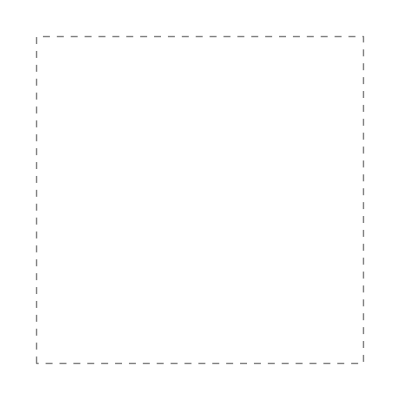

```mathematica
s0=Graphics[
{Gray,Dashed,Line[Append[vertexList,vertexList⟦1⟧]]}
,ImageSize->Tiny]
```

```mathematica
shear=0.3;
f1=F@shear
```

{{1.13845,0.0922758},{-0.207724,0.861552}}

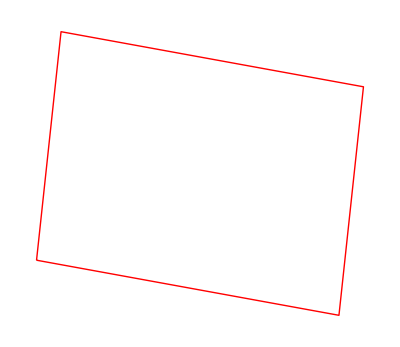

```mathematica
s1=Graphics[
{
Red,Thick,
Line[Append[
tmp=f1.#&/@vertexList;
tmp,tmp⟦1⟧
]]
}
,ImageSize->Tiny]
```

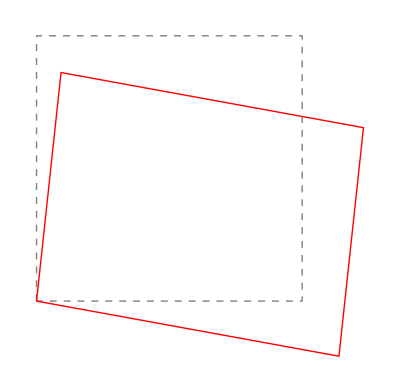

```mathematica
Show[s0,s1]
```

```mathematica
{u1,u2,v1,v2}=#@shear&/@{Subscript[eu, 1],Subscript[eu, 2],Subscript[ev, 1],Subscript[ev, 2]}
```

{{-0.992437,0.122755},{-0.122755,-0.992437},{-0.963247,0.268616},{-0.268616,-0.963247}}

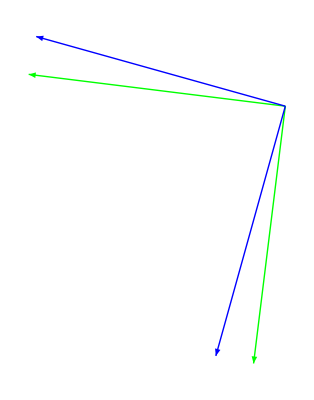

```mathematica
e1=Graphics[
{
{Green,Thin,Arrow[{{0,0},#}]}&/@{u1,u2},
{Blue,Thin,Arrow[{{0,0},#}]}&/@{v1,v2}
}
,ImageSize->Tiny]
```

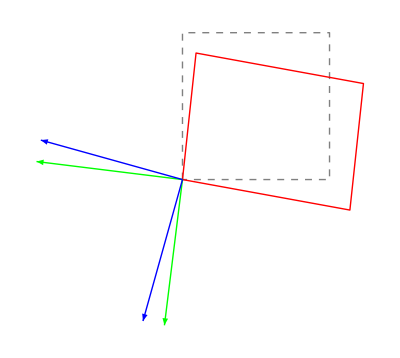

```mathematica
Show[s0,s1,e1]
```

```mathematica
Manipulate[
Show[
s0,
Graphics[
{
Red,Thick,
Line[Append[#,#⟦1⟧]&[F[γ].#&/@vertexList]]
}],
Graphics[Evaluate@{
{Green,Thin,Arrow[{{0,0},#}]}&/@{Subscript[eu, 1]@γ,Subscript[eu, 2]@γ},
{Blue,Thin,Arrow[{{0,0},#}]}&/@{Subscript[ev, 1]@γ,Subscript[ev, 2]@γ}
}]
]
,{γ,0,π/2}]
```

```mathematica
Manipulate[
Show[
s0,
Graphics[{
Red,
Thick,
Line[Append[#,#⟦1⟧]&[F[γ].#&/@vertexList]]
}],
Graphics[{
{Green,Thin,Line[{-#,#}]}&/@{Subscript[eu, 1]@γ,Subscript[eu, 2]@γ},
{Blue,Thin,Line[{-#,#}]}&/@{Subscript[ev, 1]@γ,Subscript[ev, 2]@γ}
}]
]
,{γ,0,π/2}]
```

## Visibility of Definitions With, Block, Module

```mathematica
x=.
ChebyshevT[3,x]
```

-3 x+4 x^3

```mathematica
With[{x=1},
ChebyshevT[3,x]
]
```

1

```mathematica
x=1;
Block[{x,y=2},
x=y^2;
x+y
]
```

6

```mathematica
x
```

1

```mathematica
Module[{x,y=2},
x=y^2;
x+y
]
```

6

```mathematica
$RecursionLimit
```

1024

```mathematica
inc[0]=0;
inc[i_]:=inc[i-1]+1
```

```mathematica
Block[{$RecursionLimit=20},
inc[100]
]
```

$RecursionLimit::reclim2: Recursion depth of 20 exceeded during evaluation of inc[83-1].

Hold[inc[100-1]+1]

```mathematica
inc[100]
```

100